```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
paramColumnMap=<|"H0_mean"->"H0","q0_mean"->"q0","j0_mean"->"j0","Om0_mean"->"Om0","eps_mean"->"eps","wDE0_mean"->"wDE0","wDE0p_mean"->"wDE0p"|>;
```

```mathematica
(*Build the nested association for a single model's CSV file*)
BuildModelParams[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
datasetName->Association[KeyValueMap[Function[{oldKey,newKey},newKey->assocFull[oldKey]],paramColumnMap]]]],rows]]];
```

```mathematica
(*Master nested association:allParams["Model 1"]["DESI"]-><|"H0"->...,...|>*)
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParams[file]],mcmcFiles]];
```

```mathematica
(* ============================================================*)
(*Convenience accessors*)
(* ============================================================*)

(*List available models*)
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
AvailableModels[]
```

{Model 1,Model 2,Model 3}

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
(*(*Main getter:GetParams["Model 1","DESI"]->Association of params*)
GetParams[model_String,dataset_String]:=Module[{},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
allParams[model][dataset]];

GetParams::nomodel="Model `1` not found. Available models: `2`";
GetParams::nodataset="Dataset `1` not found for `2`. Available datasets: `3`";*)
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
(*Main getter:GetParams["Model 1","DESI"]->Association of params,including "j"*)
GetParams[model_String,dataset_String]:=Module[{baseParams},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
baseParams=allParams[model][dataset];
Append[baseParams,"j"->jModelMap[model]]];
```

### Model 1:

#### Desi Values

```mathematica
params1a=GetParams["Model 1","DESI"];
params1a["q0"]
params1a["Om0"]
params1a["eps"]
params1a["H0"]
```

-0.517033

0.498537

-0.0258394

68.2919

```mathematica
(*H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;*)
```

```mathematica
params10a=GetParams["Model 1","Planck + Union3 + Pantheon+ + DESY5"];
params10a["q0"]
params10a["Om0"]
params10a["eps"]
params10a["H0"]
```

-0.516172

0.31252

0.00132349

67.7409

### Model 2:

#### Desi Values

```mathematica
params2a=GetParams["Model 2","DESI"];
params2a["q0"]
params2a["Om0"]
params2a["eps"]
params2a["H0"]
```

-0.49883

0.491401

-0.100239

68.5342

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 3:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Setup

```mathematica
zPlot=10;
zinitial=1000;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

### Obtaining q(z)

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol},
params=GetParams[model,dataset];
odeQ={dq/. j->params["j"]/. ϵ->params["eps"],q[0]==params["q0"]};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

```mathematica
qSolAllSets3["DESI"][0]
```

-0.482663

#### Model 1, All datasets

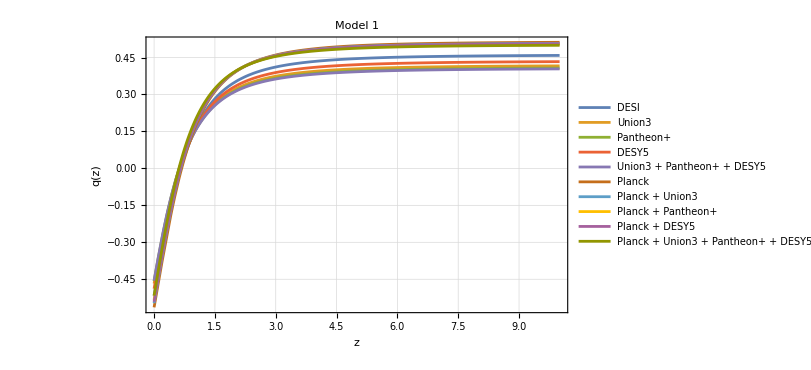

```mathematica
Plot[Evaluate[Table[qSolAllSets1[d][z],{d,Keys[qSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 2, All datasets

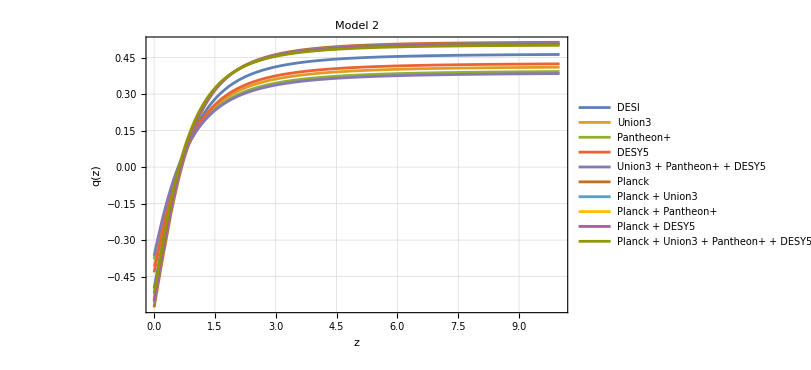

```mathematica
Plot[Evaluate[Table[qSolAllSets2[d][z],{d,Keys[qSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets2],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 3, All datasets

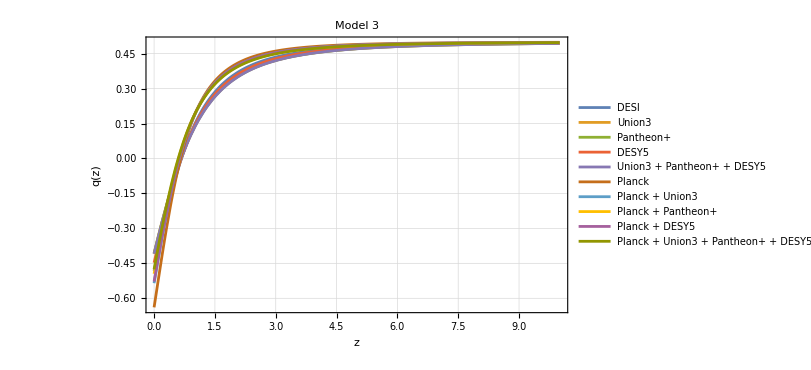

```mathematica
Plot[Evaluate[Table[qSolAllSets3[d][z],{d,Keys[qSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

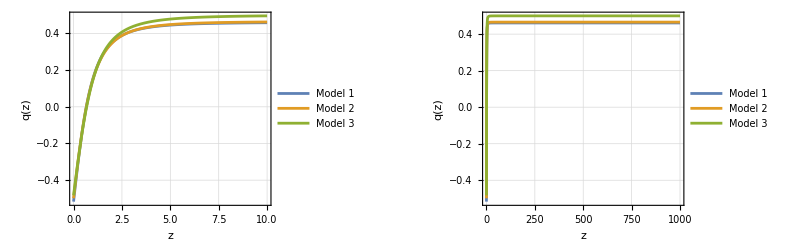

```mathematica
GraphicsRow[{
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

### Obtaining E(z)

```mathematica
SolveForEh[model_String,dataset_String]:=
Module[{params,qFn,odeEh,sol},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

odeEh={(dEh/. q->qFn)/. ϵ->params["eps"],Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

```mathematica
hSolAllSets1=Association[Map[#->SolveForEh["Model 1",#]&,AvailableDatasets["Model 1"]]];
hSolAllSets2=Association[Map[#->SolveForEh["Model 2",#]&,AvailableDatasets["Model 2"]]];
hSolAllSets3=Association[Map[#->SolveForEh["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Model 1, All datasets

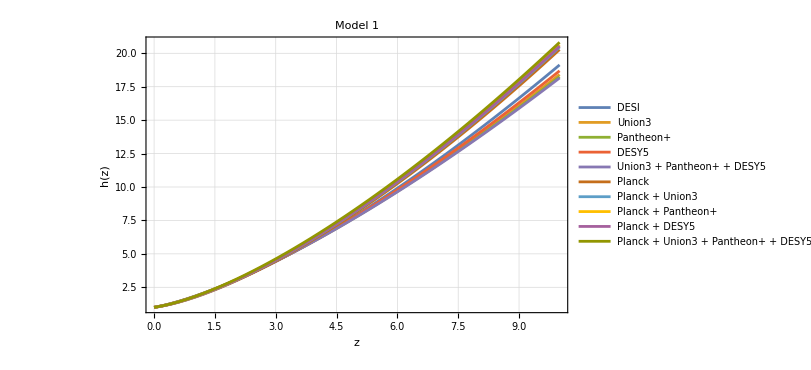

```mathematica
Plot[Evaluate[Table[hSolAllSets1[d][z],{d,Keys[hSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets1[d][zinitial]},{d,Keys[hSolAllSets1]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 13930.1
Union3 | 11069.2
Pantheon+ | 10535.5
DESY5 | 12139.7
Union3 + Pantheon+ + DESY5 | 10325.8
Planck | 18772.5
Planck + Union3 | 18564.6
Planck + Pantheon+ | 18416.3
Planck + DESY5 | 18492.5
Planck + Union3 + Pantheon+ + DESY5 | 18223.

#### Model 2, All datasets

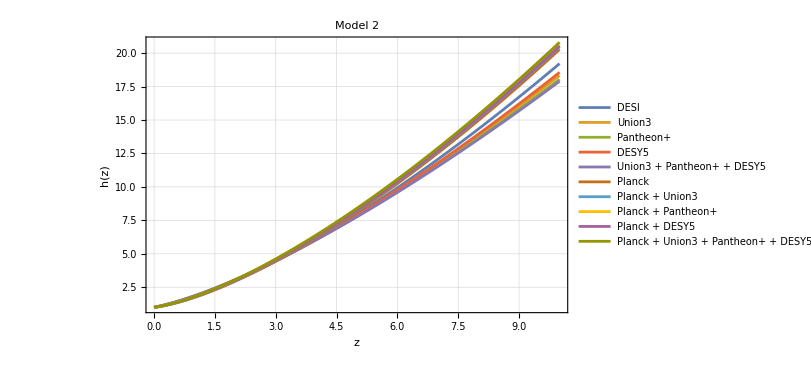

```mathematica
Plot[Evaluate[Table[hSolAllSets2[d][z],{d,Keys[hSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets2[d][zinitial]},{d,Keys[hSolAllSets2]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 14282.1
Union3 | 10781.4
Pantheon+ | 9804.99
DESY5 | 11615.
Union3 + Pantheon+ + DESY5 | 9366.95
Planck | 18842.1
Planck + Union3 | 18633.7
Planck + Pantheon+ | 18475.6
Planck + DESY5 | 18563.6
Planck + Union3 + Pantheon+ + DESY5 | 18276.6

#### Model 3, All datasets

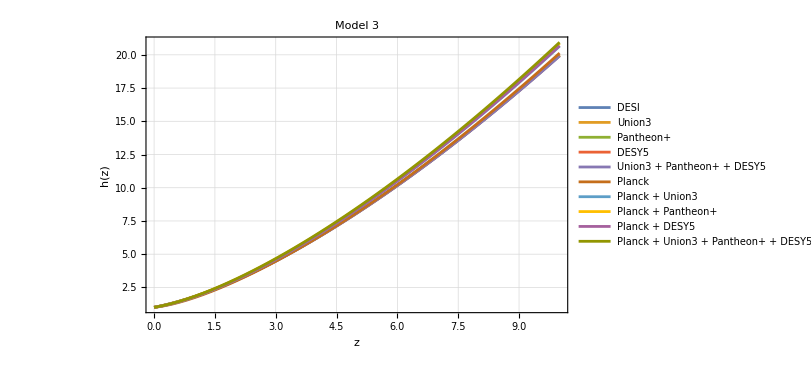

```mathematica
Plot[Evaluate[Table[hSolAllSets3[d][z],{d,Keys[hSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets3[d][zinitial]},{d,Keys[hSolAllSets3]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 17290.3
Union3 | 17316.4
Pantheon+ | 17290.3
DESY5 | 17284.6
Union3 + Pantheon+ + DESY5 | 17244.5
Planck | 17467.1
Planck + Union3 | 17917.1
Planck + Pantheon+ | 18088.
Planck + DESY5 | 17944.3
Planck + Union3 + Pantheon+ + DESY5 | 18163.1

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

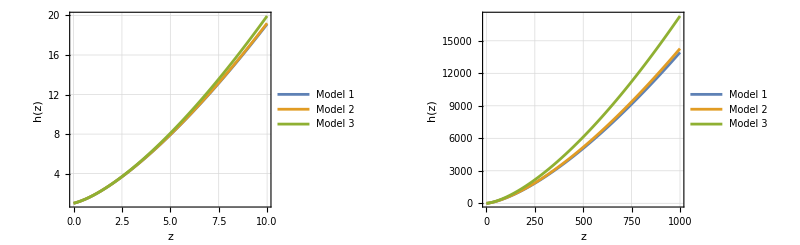

```mathematica
GraphicsRow[{
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","h(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","h(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

## Obtaining Background solution

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

1000

```mathematica
xin=-10^-14;
Ωin=0.999999997;
```

```mathematica
Table[qSolAllSets1[dataset][zinitial], {dataset,Keys[qSolAllSets3]}]
```

{0.461241,0.41875,0.409844,0.435914,0.406463,0.514422,0.509831,0.506433,0.50827,0.501985}

```mathematica
Keys[qSolAllSets3]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

#### Module

```mathematica
SolveBackground[model_String,dataset_String]:=Module[{params,qFn,z0,x0,Ω0,sol,xFn,ΩFn,domainEnd},params=GetParams[model,dataset];
If[params===$Failed,Return[$Failed]];
qFn=SolveForq[model,dataset];
If[qFn===$Failed,Return[$Failed]];
z0=zinitial;
x0=xin;
Ω0=Ωin;
Block[{q,j,s,l,ϵ},q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
(*Check where the interpolating function's domain actually ends*)domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];
<|"x"->xFn,"Ω"->ΩFn,"z0"->z0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None]|>];
```

### Model 1, All datasets

```mathematica
bgResultsModel1=Association[Map[#->SolveBackground["Model 1",#]&,AvailableDatasets["Model 1"]]];
```

DESI is stiff/diverges at z ≃ 113.991

Union3 is stiff/diverges at z ≃ 144.78

Pantheon+ is stiff/diverges at z ≃ 149.852

DESY5 is stiff/diverges at z ≃ 133.952

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 151.698

```mathematica
(*Summary table:dataset,qin,did it fail,at what z*)
Grid[Prepend[Table[{dataset,qSolAllSets1[dataset][zinitial],bgResultsModel1[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","q_in","Failed at z"}],Frame->All]
```

Dataset | q_in | Failed at z
DESI | 0.461241 | 113.991
Union3 | 0.41875 | 144.78
Pantheon+ | 0.409844 | 149.852
DESY5 | 0.435914 | 133.952
Union3 + Pantheon+ + DESY5 | 0.406463 | 151.698
Planck | 0.514422 | None
Planck + Union3 | 0.509831 | None
Planck + Pantheon+ | 0.506433 | None
Planck + DESY5 | 0.50827 | None
Planck + Union3 + Pantheon+ + DESY5 | 0.501985 | None

#### Plotting for converging solutions

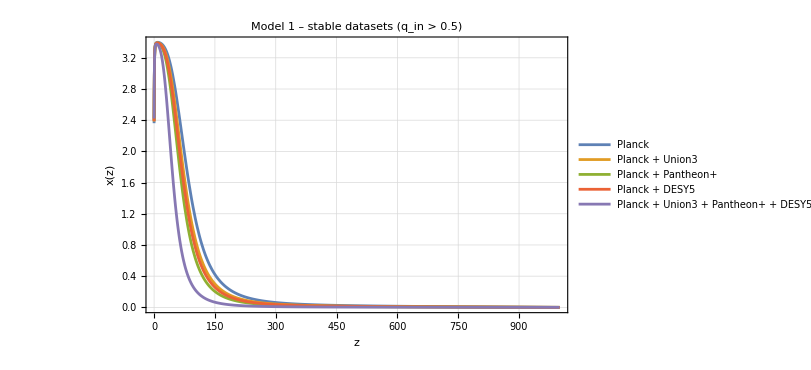

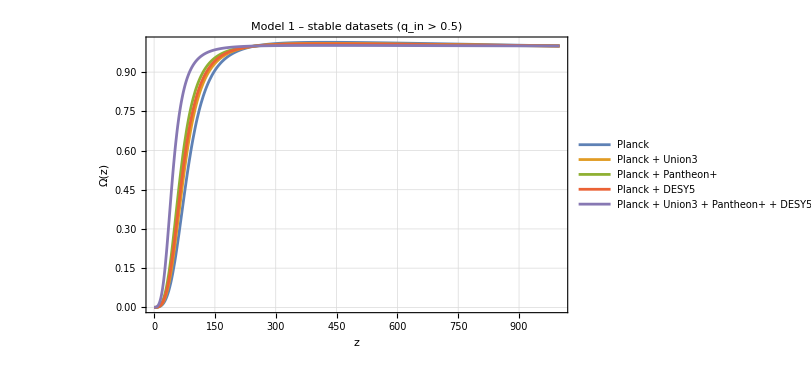

```mathematica
okDatasets=Select[AvailableDatasets["Model 1"],bgResultsModel1[#]["failedAtZ"]===None&];

(*Plot 3:successful datasets,z=0 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["x"][z],{d,okDatasets}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 1 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot 4:successful datasets,z=0 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["Ω"][z],{d,okDatasets}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 1 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

#### Plotting for converging solutions

```mathematica
failedDatasets=Select[AvailableDatasets["Model 1"],bgResultsModel1[#]["failedAtZ"]=!=None&];
```

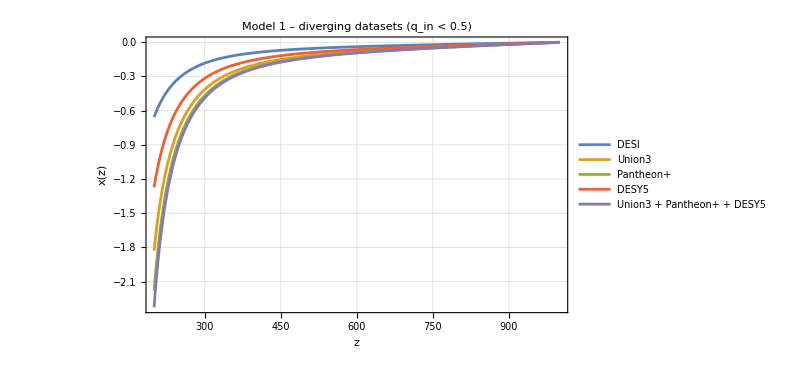

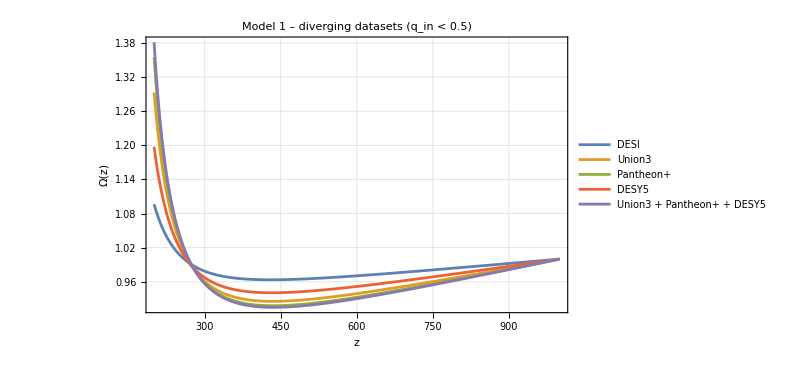

```mathematica
failedDatasets=Select[AvailableDatasets["Model 1"],bgResultsModel1[#]["failedAtZ"]=!=None&];
(*Plot 1:failed datasets,z=200 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["x"][z],{d,failedDatasets}]],{z,200,1000},PlotLegends->Placed[LineLegend[failedDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot 2:failed datasets,z=200 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel1[d]["Ω"][z],{d,failedDatasets}]],{z,200,1000},PlotLegends->Placed[LineLegend[failedDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

### Model 2, All datasets

```mathematica
bgResultsModel2=Association[Map[#->SolveBackground["Model 2",#]&,AvailableDatasets["Model 2"]]];
```

DESI is stiff/diverges at z ≃ 109.564

Union3 is stiff/diverges at z ≃ 147.522

Pantheon+ is stiff/diverges at z ≃ 156.914

DESY5 is stiff/diverges at z ≃ 139.326

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 161.048

```mathematica
(*Summary table:dataset,qin,did it fail,at what z*)
Grid[Prepend[Table[{dataset,qSolAllSets2[dataset][zinitial],bgResultsModel2[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","q_in","Failed at z"}],Frame->All]
```

Dataset | q_in | Failed at z
DESI | 0.465807 | 109.564
Union3 | 0.414006 | 147.522
Pantheon+ | 0.3965 | 156.914
DESY5 | 0.427707 | 139.326
Union3 + Pantheon+ + DESY5 | 0.388171 | 161.048
Planck | 0.515242 | None
Planck + Union3 | 0.510744 | None
Planck + Pantheon+ | 0.507314 | None
Planck + DESY5 | 0.509236 | None
Planck + Union3 + Pantheon+ + DESY5 | 0.502783 | None

#### Plotting for converging solutions

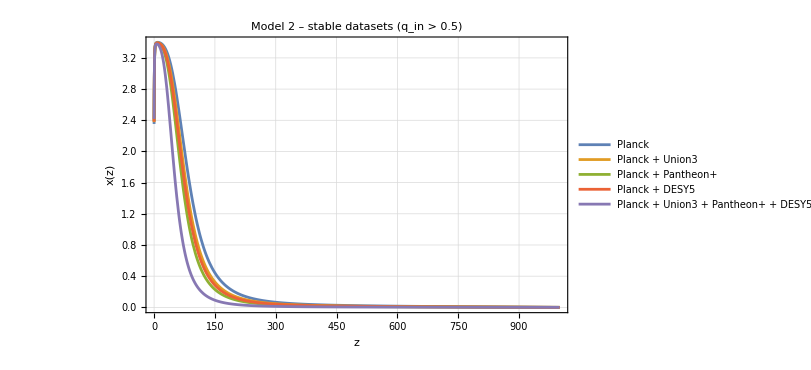

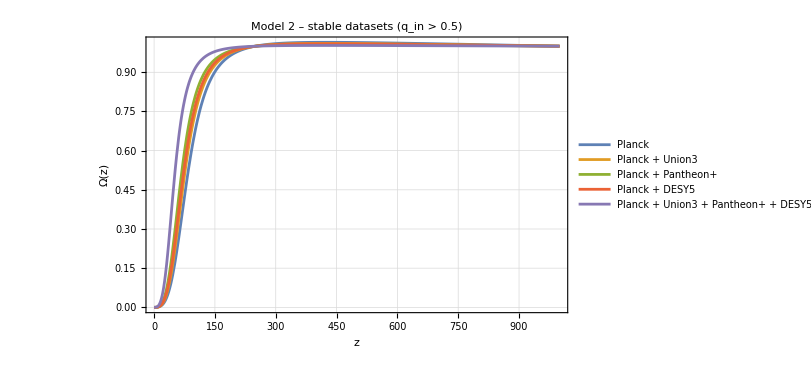

```mathematica
okDatasets=Select[AvailableDatasets["Model 2"],bgResultsModel2[#]["failedAtZ"]===None&];

(*Plot: successful datasets,z=0 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel2[d]["x"][z],{d,okDatasets}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 2 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot: successful datasets,z=0 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel2[d]["Ω"][z],{d,okDatasets}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 2 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

#### Plotting for converging solutions

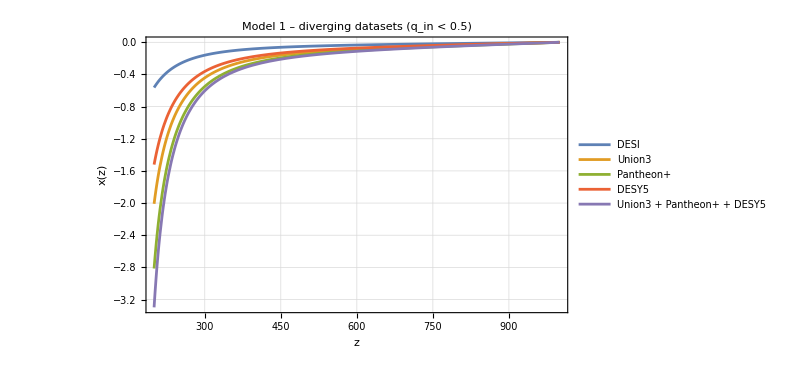

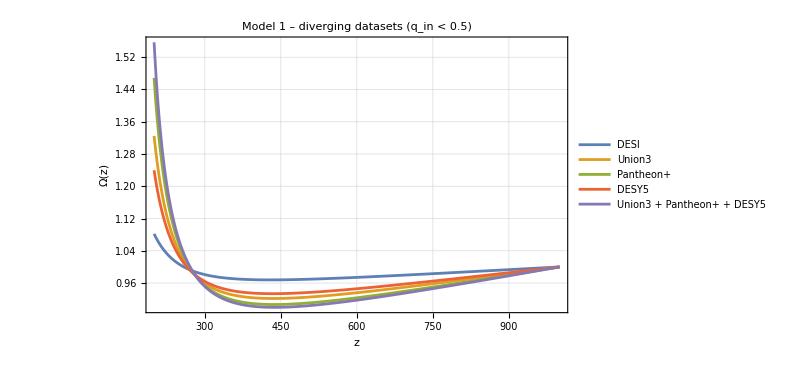

```mathematica
failedDatasets=Select[AvailableDatasets["Model 2"],bgResultsModel1[#]["failedAtZ"]=!=None&];

(*Plot 1:failed datasets,z=200 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel2[d]["x"][z],{d,failedDatasets}]],{z,200,1000},PlotLegends->Placed[LineLegend[failedDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot 2:failed datasets,z=200 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel2[d]["Ω"][z],{d,failedDatasets}]],{z,200,1000},PlotLegends->Placed[LineLegend[failedDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

### Model 3, All datasets

```mathematica
bgResultsModel3=Association[Map[#->SolveBackground["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

DESI is stiff/diverges at z ≃ 0.79141

Union3 is stiff/diverges at z ≃ 1.97069

Pantheon+ is stiff/diverges at z ≃ 1.98836

DESY5 is stiff/diverges at z ≃ 1.37368

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 2.02071

```mathematica
qSolAllSets3[AvailableDatasets["Model 3"][[1]]][zinitial]
```

0.5

```mathematica
(*Summary table:dataset,qin,did it fail,at what z*)
Grid[Prepend[Table[{dataset,qSolAllSets3[dataset][zinitial],bgResultsModel3[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","q_in","Failed at z"}],Frame->All]
```

Dataset | q_in | Failed at z
DESI | 0.5 | 0.79141
Union3 | 0.5 | 1.97069
Pantheon+ | 0.5 | 1.98836
DESY5 | 0.5 | 1.37368
Union3 + Pantheon+ + DESY5 | 0.5 | 2.02071
Planck | 0.5 | None
Planck + Union3 | 0.5 | None
Planck + Pantheon+ | 0.5 | None
Planck + DESY5 | 0.5 | None
Planck + Union3 + Pantheon+ + DESY5 | 0.5 | None

#### Plotting for converging solutions

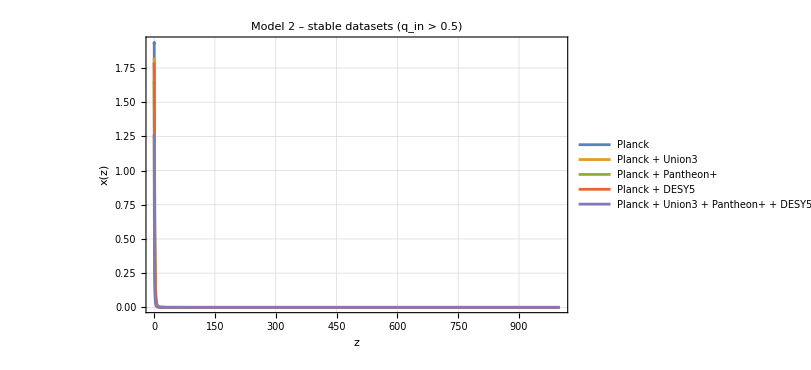

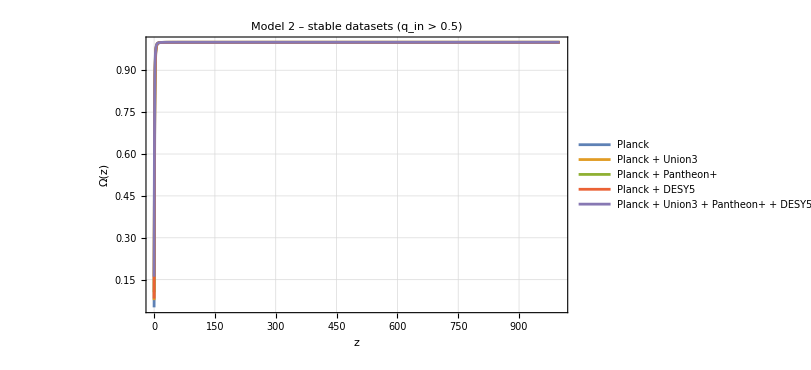

```mathematica
okDatasets3=Select[AvailableDatasets["Model 3"],bgResultsModel3[#]["failedAtZ"]===None&];

(*Plot: successful datasets,z=0 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel3[d]["x"][z],{d,okDatasets3}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets3,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 2 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot: successful datasets,z=0 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel3[d]["Ω"][z],{d,okDatasets3}]],{z,0,1000},PlotLegends->Placed[LineLegend[okDatasets,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 2 – stable datasets (q_in > 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

#### Plotting for converging solutions

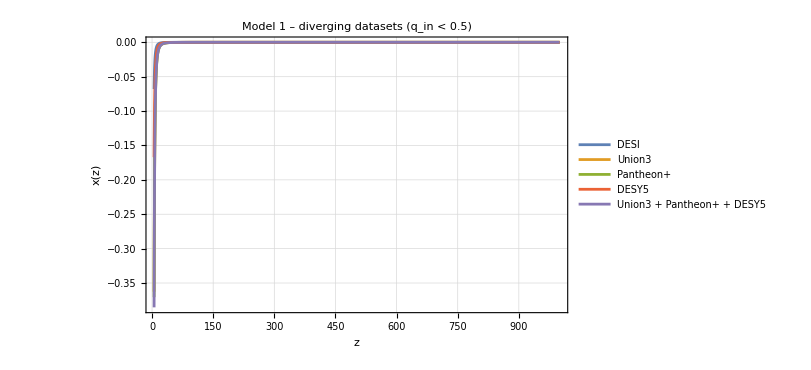

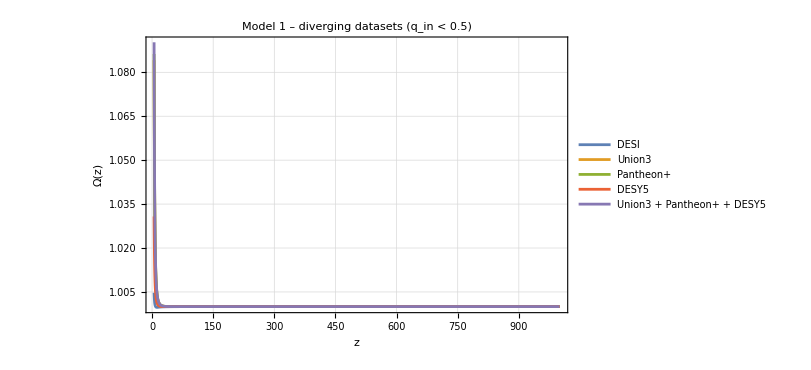

```mathematica
failedDatasets3=Select[AvailableDatasets["Model 3"],bgResultsModel3[#]["failedAtZ"]=!=None&];

(*Plot 1:failed datasets,z=200 to 1000,x(z)*)
Plot[Evaluate[Table[bgResultsModel3[d]["x"][z],{d,failedDatasets3}]],{z,5,1000},PlotLegends->Placed[LineLegend[failedDatasets3,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","x(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]

(*Plot 2:failed datasets,z=200 to 1000,Ω(z)*)
Plot[Evaluate[Table[bgResultsModel3[d]["Ω"][z],{d,failedDatasets3}]],{z,5,1000},PlotLegends->Placed[LineLegend[failedDatasets3,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.2}],Frame->True,FrameLabel->{"z","Ω(z)"},PlotLabel->"Model 1 – diverging datasets (q_in < 0.5)",GridLines->Automatic,PlotRange->All,ImageSize->600]
```

## Comparing to 21cm paper

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

1000

```mathematica
xin=-10^-14;
Ωin=0.999999997;
```

```mathematica
qin=0.499999996;
Ehin=17346.495;
```

### Model 1

#### Obtaining E(z) and q(z)

```mathematica
params10a["eps"]
```

0.00132349

```mathematica
solq21=NDSolve[{dq/.j->j1/.ϵ->params10a["eps"], q[zinitial]==qin},q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

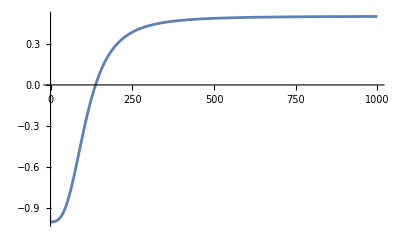

```mathematica
Plot[q[z]/.solq21, {z,0,zinitial}, PlotRange->All]
```

```mathematica
solq21
```

{q→InterpolatingFunction[…]}

```mathematica
dEh/.j->j1/.ϵ->params10a["eps"]/.solq21
```

-Eh[z] (1+InterpolatingFunction[…][z])+(1+z) Eh'[z]==0

```mathematica
solEh21=NDSolve[{dEh/.j->j1/.ϵ->params10a["eps"]/.solq21, Eh[zinitial]==Ehin},Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

```mathematica
Eh[0]/.solEh21
```

630.647

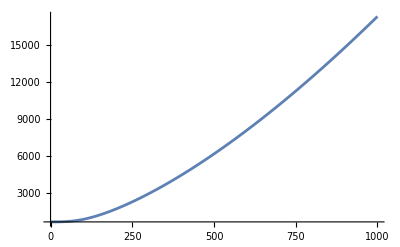

```mathematica
Plot[Eh[z]/.solEh21, {z,0,zinitial}, PlotRange->All]
```